## Wprowadzenie do programu MATHEMATICA

## 1. Czyszczenie wszystkich wprowadzonych definicji i podstawień.

### Instrukcja, którą warto umieszczać na początku każdego notebooka:

```mathematica
ClearAll["Global`*"];
```

## 2. Zapis liczb dziesiętnych.

### Liczby dziesiętne zapisujemy z kropką!

```mathematica
3.25
```

3.25

### Zapis liczby dziesiętnej z przecinkiem powoduje pojawienie się komunikatu o błędzie:

```mathematica
3,25
```

Syntax::tsntxi: "3,25" is incomplete; more input is needed.

## 3. Działania arytmetyczne.

### Dodawanie:

```mathematica
5+7
```

12

### Odejmowanie:

```mathematica
5-2
```

3

### Mnożenie:

```mathematica
5*4
```

20

```mathematica
5×4
```

20

### Dzielenie:

```mathematica
15/3
```

5

```mathematica
15/3
```

5

### Potęgowanie:

```mathematica
3^2
```

9

```mathematica
3^2
```

9

## 4. Przybliżenie numeryczne.

```mathematica
6/4
```

3/2

```mathematica
6/4//N
```

1.5

### Przybliżenie numeryczne z podaniem liczby cyfr (w przykładzie 50):

```mathematica
N[π,50]
```

3.1415926535897932384626433832795028841971693993751

## 5. Przypisanie wartości zmiennym.

```mathematica
x=2
(* aktualna wartość x *) x
```

2

2

```mathematica
x=2
x=3
(* aktualna wartość x *) x
```

2

3

3

```mathematica
x=2
x=3
(* kasowanie podstawienia *)x=.
(* aktualna wartość x *) x
```

2

3

x

```mathematica
a+b/. a-> 2
```

2+b

```mathematica
a+b/. {a-> 1,b->5}
```

6

## 6. Korzystanie z palet.

### Palety (menu Palettes) zawierają symbole, które można kopiować do notebooka:

## 7. Wybrane funkcje matematyczne.

### Pierwiastek kwadratowy:

```mathematica
Sqrt[9]
```

3

```mathematica
√9
```

3

### Wartość bezwzględna z liczby:

```mathematica
Abs[-5]
```

5

### Funkcja wykładnicza (eksponencjalna):

```mathematica
Exp[1]
```

ⅇ

```mathematica
ⅇ^1
```

ⅇ

```mathematica
ⅇ^1//N
```

2.71828

### Logarytm naturalny (w przykładzie z e^2):

```mathematica
Log[ⅇ^2]
```

2

### Logarytm dziesiętny (w przykładzie z 1000):

```mathematica
Log10[1000]
```

3

### Logarytm o dowolnej podstawie (w przykładzie o podstawie 7 z 49):

```mathematica
Log[7,49]
```

2

### Funkcja kosinus (w przykładzie dla 20 stopni):

```mathematica
Cos[20°]//N
```

0.939693

### Funkcja sinus (w przykładzie dla 20 stopni):

```mathematica
Sin[20°]//N
```

0.34202

### Funkcja tangens (w przykładzie dla 20 stopni):

```mathematica
Tan[20°]//N
```

0.36397

### Funkcja kotangens (w przykładzie dla 20 stopni):

```mathematica
Cot[20°]//N
```

2.74748

### Funkcje odwrotne do funkcji trygonometrycznych (w przykładzie dla 1, wartość w radianach):

```mathematica
ArcSin[1]
```

π/2

```mathematica
ArcCos[1]
```

0

```mathematica
ArcTan[1]
```

π/4

```mathematica
ArcCot[1]
```

π/4

## 8. Pochodne ( w przykładach po zmiennej x).

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
D[x^3, x]
```

3 x^2

```mathematica
D[Log[x], x]
```

1/x

```mathematica
D[(Cos[x]×Sin[x])^4/(x^3+x^2), x]
```

(4 Cos[x]^5 Sin[x]^3)/(x^2+x^3)-((2 x+3 x^2) Cos[x]^4 Sin[x]^4)/((x^2+x^3)^2)-(4 Cos[x]^3 Sin[x]^5)/(x^2+x^3)

```mathematica
D[(x^2*y^3), x]
```

2 x y^3

## 9. Pochodne drugiego rzędu ( w przykładach po zmiennej x).

```mathematica
D[(x^3), x,x]
```

6 x

```mathematica
D[(x^2*y^3), x,x]
```

2 y^3

```mathematica
D[(Cos[x]*y^3), x,x]
```

-y^3 Cos[x]

## 9. Całka nieoznaczona ( w przykładach po zmiennej x).

```mathematica
∫x^n ⅆx
```

x^(1+n)/(1+n)

```mathematica
∫x^2 ⅆx
```

x^3/3

```mathematica
∫D[x^3, x]ⅆx
```

x^3

```mathematica
∫-Sin[x]ⅆx
```

Cos[x]

```mathematica
∫Cos[x]ⅆx
```

Sin[x]

```mathematica
∫1/x ⅆx
```

Log[x]

```mathematica
∫Cos[x]×Sin[x]ⅆx
```

-1/2 Cos[x]^2

```mathematica
∫Cos[x]×Sin[x]ⅆx
```

-1/2 Cos[x]^2

## 10. Całka oznaczona ( w przykładach po zmiennej x).

```mathematica
∫_0^1 x^2 ⅆx
```

1/3

```mathematica
∫_-1^1 x^2 ⅆx
```

2/3

```mathematica
∫_0^π Cos[x]ⅆx
```

0

```mathematica
∫_0^π Sin[x]ⅆx
```

2

```mathematica
∫_0^(π/2) Cos[x]ⅆx
```

1

```mathematica
∫_0^(π/2) Sin[x]ⅆx
```

1

```mathematica
∫_0^(2×π) Cos[x]ⅆx
```

0

```mathematica
∫_0^(2×π) Sin[x]ⅆx
```

0

```mathematica
∫_(-π/2)^(π/2) Cos[x]ⅆx
```

2

```mathematica
∫_(-π/2)^(π/2) Sin[x]ⅆx
```

0

## 11. Rozwiązywanie równań ( w przykładach z niewiadomą x).

```mathematica
rown1=Solve[x^2+6==8,x]
```

{{x→-√2},{x→√2}}

```mathematica
(* postać macierzowa zbioru rozwiązań *) MatrixForm[rown1]
```

(x→-√2
x→√2)

## 12. Rozwiązywanie układów równań ( w przykładach z niewiadomymi x oraz y).

```mathematica
rown2=Solve[{x^2+y^2==8,y-2*x==6},{x,y}]
```

{{x→-14/5,y→2/5},{x→-2,y→2}}

```mathematica
(* postać macierzowa zbioru rozwiązań *) MatrixForm[rown2]
```

(x→-14/5 | y→2/5
x→-2 | y→2)

### Podstawienie rozwiązań układu równań “rown2” do nowych zmiennych. Położenie elementu w macierzy wyznacza numer wiersza i numer kolumny w jakich dany element się znajduje:

```mathematica
x1=x/. rown2[[1,1]]
```

-14/5

```mathematica
x2=x/. rown2[[2,1]]
```

-2

```mathematica
y1=y/. rown2[[1,2]]
```

2/5

```mathematica
x2=y/. rown2[[2,2]]
```

2

## 13. Tworzenie wykresów dwuwymiarowych.

### Podstawowa instrukcja (wykres funkcji y = 2 x^2 w przedziale x od -5 do 10):

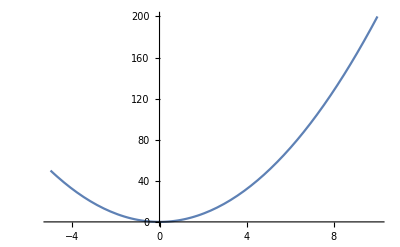

```mathematica
Plot[2*x^2,{x,-5,10}]
```

### Wybieramy czcionkę:

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12}]
```

-Graphics-

### Określamy kolor i grubość wykresu:

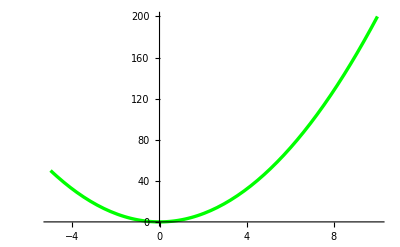

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{Green,Thickness[0.006]}]
```

### Dodajemy opis osi:

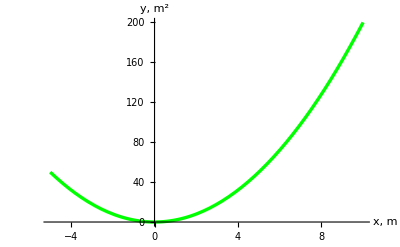

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{Green,Thickness[0.006]},AxesLabel->{"x, m","y, m^2"}]
```

### Wstawiamy nazwę rysunku:

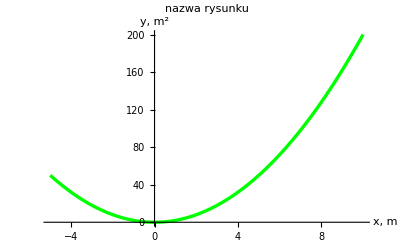

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{Green,Thickness[0.006]},AxesLabel->{"x, m","y, m^2"},PlotLabel->"nazwa rysunku"]
```